```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/3v_Moments

## Get Matrices

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];

IDXFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,ii}],{ii,0,n}],1];
IDXFullOdd[M_]:=Select[IDXFull[M],(OddQ[#⟦1⟧])&];
IDXFullEven[M_]:=Select[IDXFull[M],(EvenQ[#⟦2⟧])&];

IDXFull2D[M_]:=Select[IDXFull[M],(EvenQ[#⟦3⟧])&];

TotalVar[M_]:=Total[Table[Length[IDXFull2D[ii]],{ii,0,M}]];

IDXFull2DOdd[M_]:=Select[Select[IDXFull[M],(EvenQ[#⟦3⟧])&],(OddQ[#⟦1⟧])&];
IDXFull2DEven[M_]:=Select[Select[IDXFull[M],(EvenQ[#⟦3⟧])&],(OddQ[#⟦2⟧])&];

DevelopBCWall[bc_,var_]:=Module[{rhoW,bCond,rhoWSol},

bCond = (bc.var-bc⟦All,1⟧rhoW)/.{w[1,0,0]->0};
rhoWSol = Solve[bCond⟦1⟧==0,rhoW]⟦1⟧;
bCond = bCond/.rhoWSol;
bCond⟦1⟧=w[1,0,0];
bCond = CoefficientArrays[Table[ii==0,{ii,bCond}],var]⟦2⟧;

Simplify[bCond]

]

GetAoe[Ax_,var_]:=Ax⟦Flatten[Position[var,Alternatives@@Select[var,(OddQ[#⟦1⟧])&]]],Flatten[Position[var,Alternatives@@Select[var,(EvenQ[#⟦1⟧])&]]]⟧;

(*truncate matrices for better convergence*)
TruncateMat[Ax_,B_,P_,Sigma_,M_]:=Module[{var,varTrun,loc},

var = Flatten[Table[IDXFull2D[ii],{ii,0,M}],1];
varTrun = Flatten[{Flatten[Table[IDXFull2D[ii],{ii,0,M-1}],1],IDXFull2DOdd[M]},1];

loc = Flatten[Position[var,Alternatives@@varTrun]];

{Ax⟦loc,loc⟧,B⟦All,loc⟧,P⟦loc,loc⟧,Sigma⟦loc,All⟧,varTrun}
]

GetProduction[var_]:=Module[{P,W200,W020,W002},

W200 = Flatten[Position[var,w[2,0,0]]];
W020 = Flatten[Position[var,w[0,2,0]]];
W002 = Flatten[Position[var,w[0,0,2]]];

P = DiagonalMatrix[Table[1,{ii,1,Length[var]}]];

P⟦W200,{W200⟦1⟧,W020⟦1⟧,W002⟦1⟧}⟧ = -{-2/3,1/3,1/3};
P⟦W020,{W200⟦1⟧,W020⟦1⟧,W002⟦1⟧}⟧ = -{1/3,-2/3,1/3};
P⟦W002,{W200⟦1⟧,W020⟦1⟧,W002⟦1⟧}⟧ = -{1/3,1/3,-2/3};

P⟦{1,2,3},{1,2,3}⟧=0;

P

]
StabilizeBoundary[Ax_,B_,varIdx_,M_]:=Module[{varOdd,varEven,Aoe,Boe,Btemp,MatOnsager},

varOdd = Flatten[Position[varIdx,Alternatives@@Select[varIdx,(OddQ[#⟦1⟧])&]]];
varEven = Flatten[Position[varIdx,Alternatives@@Select[varIdx,(EvenQ[#⟦1⟧])&]]];

Aoe = Ax⟦varOdd,varEven⟧;

(*A factor of 2 from the left has already been included. *)
Boe = -B⟦All,varEven⟧;

(*Mat Onsager*)
MatOnsager = Boe⟦All,1;;Length[varOdd]⟧.Inverse[Aoe⟦All,1;;Length[varOdd]⟧];

(*stabilize Boe*)
Boe = MatOnsager.Aoe;

Btemp = B;
Btemp⟦All,varOdd⟧ = IdentityMatrix[Length[varOdd]];
Btemp⟦All,varEven⟧ = -Boe;

Btemp
]
```

```mathematica
GetMatrixHermite[M_]:=Module[{varIdxComplete,Ax,Ay,ia,ja,va,numVar,indexMinus,indexPlus,data,EvenCat3,OddVar,EvenVar,intEven,idxOdd,var,bc,filenameAx,filenameB,P,Sigma,filenameP,filenameSigma,filenameOddID,bcInflow},

(*all the idx. Already converted to 2D*)
varIdxComplete = Flatten[Table[IDXFull2D[ii],{ii,0,M}],1];

var = Map[Apply[w,#]&,varIdxComplete];
OddVar = Select[varIdxComplete,(OddQ[#⟦1⟧])&];
numVar = Length[varIdxComplete];

ia = ConstantArray[0,{numVar-Length[IDXFull2D[M]]}];
ja = ConstantArray[0,{numVar-Length[IDXFull2D[M]]}];
va = ConstantArray[0,{numVar-Length[IDXFull2D[M]]}];

Do[
ia⟦ii⟧ = ii;

indexPlus = {varIdxComplete⟦ii⟧⟦1⟧+1,varIdxComplete⟦ii⟧⟦2⟧,varIdxComplete⟦ii⟧⟦3⟧};

ja⟦ii⟧ = Flatten[Position[varIdxComplete,indexPlus]]⟦1⟧;
va⟦ii⟧ = Sqrt[varIdxComplete⟦ii⟧⟦1⟧+1];

,{ii,1,numVar-Length[IDXFull2D[M]]}];

(*account for the symmetry of the matrix*)
data = Flatten[{Table[{ia⟦ii⟧,ja⟦ii⟧}->va⟦ii⟧,{ii,1,Length[ia]}],Table[{ja⟦ii⟧,ia⟦ii⟧}->va⟦ii⟧,{ii,1,Length[ia]}]},1];

Ax = SparseArray[data,{numVar,numVar}];

(*create Ay*)
ia = ConstantArray[0,{numVar-Length[IDXFull2D[M]]}];
ja = ConstantArray[0,{numVar-Length[IDXFull2D[M]]}];
va = ConstantArray[0,{numVar-Length[IDXFull2D[M]]}];
Do[
ia⟦ii⟧ = ii;

indexPlus = {varIdxComplete⟦ii⟧⟦1⟧,varIdxComplete⟦ii⟧⟦2⟧+1,varIdxComplete⟦ii⟧⟦3⟧};

ja⟦ii⟧ = Flatten[Position[varIdxComplete,indexPlus]]⟦1⟧;
va⟦ii⟧ = Sqrt[varIdxComplete⟦ii⟧⟦2⟧+1];

,{ii,1,numVar-Length[IDXFull2D[M]]}];

(*account for the symmetry of the matrix*)
data = Flatten[{Table[{ia⟦ii⟧,ja⟦ii⟧}->va⟦ii⟧,{ii,1,Length[ia]}],Table[{ja⟦ii⟧,ia⟦ii⟧}->va⟦ii⟧,{ii,1,Length[ia]}]},1];

Ay = SparseArray[data,{numVar,numVar}];

intEven = ConstantArray[0,{Length[OddVar],1}];

Do[
EvenVar = Select[varIdxComplete,(#⟦2⟧==OddVar⟦ii⟧⟦2⟧&&#⟦3⟧==OddVar⟦ii⟧⟦3⟧&&EvenQ[#⟦1⟧])&];

intEven⟦ii⟧=Table[HSpcInt[OddVar⟦ii⟧⟦1⟧,jj⟦1⟧],{jj,EvenVar}].Map[Apply[w,#]&,EvenVar];
,{ii,1,Length[OddVar]}];

intEven = Map[Apply[w,#]&,OddVar]-2intEven;
bc = CoefficientArrays[Table[ii==0,{ii,intEven}],var]⟦2⟧;
bcInflow = bc;

bc = DevelopBCWall[bc,var];

bc = StabilizeBoundary[Ax,bc,varIdxComplete,M];
bcInflow = StabilizeBoundary[Ax,bcInflow,varIdxComplete,M];

P= GetProduction[var];

{Ax,bc,P}
]
```

## Develop The projection matrix

```mathematica
ProjectorHermite[M_]:=Module[{varIdx,swapVarIdx,locationSwaped,Proj},

varIdx = Flatten[Table[IDXFull2D[ii],{ii,0,M}],1];

Proj = ConstantArray[0,{Length[varIdx],Length[varIdx]}];

Do[Proj⟦ii,ii⟧=(-1)^(varIdx⟦ii⟧⟦1⟧)(-1)^(varIdx⟦ii⟧⟦2⟧);,{ii,1,Length[varIdx]}];

Proj

]
```

## Manufactured Solution

```mathematica
GetForce[M_]:=Module[{Ax,Bid1,P,Proj,Bid3,U,force,gid1,gid2},

{Ax,Bid1,P} =GetMatrixHermite[M];
P=P/0.1;
Proj = ProjectorHermite[M];
Bid3 = Bid1.Proj;

U=Flatten[ConstantArray[0,{Length[Ax],1}]];

U⟦4⟧=Cos[π x]Sin[π t];
U⟦6⟧=Cos[π x]Sin[π t];
U⟦7⟧=Cos[π x]Sin[π t];

force = D[U,t]+Ax.D[U,x]-P.U;

gid1 = Bid1.U/.{x->1};
gid2 = Bid3.U/.{x->0};

{force,gid1,gid2,U}
]
```

```mathematica
CForm[GetForce[4]⟦1⟧⟦10⟧]
```

0. - Pi*Sin(Pi*t)*Sin(Pi*x)

```mathematica
GetForce[4]⟦1⟧//MatrixForm
```

(0.
0.-√2 π Sin[π t] Sin[π x]
0.
0.+π Cos[π t] Cos[π x]
0.
0.+π Cos[π t] Cos[π x]
0.+π Cos[π t] Cos[π x]
0.-√3 π Sin[π t] Sin[π x]
0.
0.-π Sin[π t] Sin[π x]
0.-π Sin[π t] Sin[π x]
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

## Convergence Plots

```mathematica
h = {22/176,22/352,22/704,22/1408,22/2816,22/5632,22/11264};
error={0.29816,0.196354,0.114863,0.0624901,0.0326615,0.0167106,0.00845458};
```

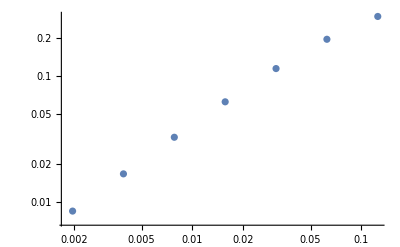

```mathematica
ListLogLogPlot[Transpose[{h,error}]]
```